```mathematica
f[x_,y_,t_,xm_,ym_]:=Sin[(x-xm/2)/xm*2Pi Cos[t]]/16+Sin[(y-ym/2)/ym*2Pi Sin[t]]/16+0.125+7*Exp[-(x-xm/2)^2/100-(y-ym/2)^2/100]/8
```

```mathematica
values[t_,xm_,ym_]:=ParallelTable[f[x,y,t,xm,ym],{x,0,xm},{y,0,ym}];
ranges[t_,xm_,ym_]:=Module[{v,m,M},v=values[t,xm,ym];m=Parallelize[Min[v]];M=Parallelize[Max[v]];{{t,m},{t,M}}];
```

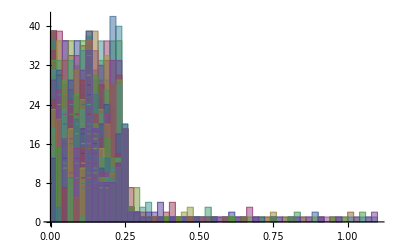

```mathematica
Histogram[values[1,64,128]]
```

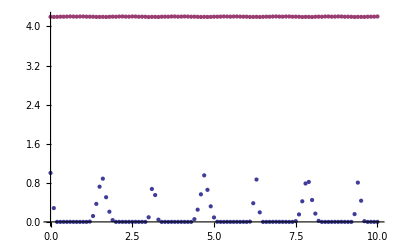

```mathematica
ListPlot[Transpose[Table[ranges[t],{t,0,10,0.1}]]]
```

```mathematica
Animate[ArrayPlot[values[t,64,128],ColorFunction->"SunsetColors"],{t,0,3}]
```